# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
(*SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];*)
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

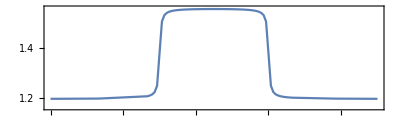

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

Rerun everything

```mathematica
bcscompilecssrerun={};
```

```mathematica
τ=0.
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
τ+=δ;
AppendTo[bcscompilecssrerun,{τ,δ,res}];
DumpSave["bcscompilecssrerun.mx",bcscompilecssrerun];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz/.CustomGatesDraw,5];
,{δ,δτ}];
```

0.

**** Compile @Thu 29 Dec 2022 09:47:33 τ=0.; δ0 ****

Set::shape: Lists {time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,«4»} and CJRecompile[5,{{1.,0,0,0,0,0,0,0,0,0,«22»},{0,1.,0,0,0,0,0,0,0,0,«22»},{0,0,1.,0,0,0,0,0,0,0,«22»},{0,0,0,1.,0,0,0,0,0,0,«22»},{0,0,0,0,1.,0,0,0,0,0,«22»},{0,0,0,0,0,1.,0,0,0,0,«22»},{0,0,0,0,0,0,1.,0,0,0,«22»},{0,0,0,0,0,0,0,1.,0,0,«22»},{0,0,0,0,0,0,0,0,1.,0,«22»},{0,0,0,0,0,0,0,0,0,1.,«22»},«22»},DefaultConfig[5,{1,2,4,8,16}]] are not the same shape.

τ=0.; δ=0; cost=Ecur; ngates=0; runtime=time

-Graphics-

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed

**** Compile @Thu 29 Dec 2022 09:47:34 τ=0.; δ4. ****

Set::shape: Lists {time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,«4»} and CJRecompile[5,{{-0.684274+0.729225 ⅈ,0,0,0,0,0,0,0,0,0,«22»},{0,0.755544-0.164603 ⅈ,0.239335+0.384539 ⅈ,0,0.283821+0.208892 ⅈ,0,0,0,0.232764+0.0541091 ⅈ,0,«22»},«8»,«22»},DefaultConfig[5,{1,2,4,8,16}]] are not the same shape.

τ=4.; δ=4.; cost=Ecur; ngates=0; runtime=time

-Graphics-

DrawCircuit::error: Invalid arguments. See ?DrawCircuit

$Failed

**** Compile @Thu 29 Dec 2022 09:47:34 τ=4.; δ4. ****

$Aborted

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,res}=comp;
ApplyCircuit[ψexact,res[[4]]/.CustomGatesDefinitions/.res[[5]]];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bcscompilecss2}];
```

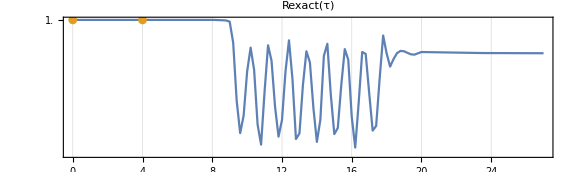

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```